#### [Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x+y/2) ψ_-α*(x-y/2) ⅆy (Wikipedia convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
(* For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x) *)
Ws1s2[α_,θ_,x_,p_,s1_,s2_]:=FullSimplify[1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[s1 √2 α Cos[θ],s1 √2 α Sin[θ],x+y/2]ψ[s2 √2 α Cos[θ],-s2 √2 α Sin[θ],x-y/2]ⅆy];
Ws1s2[α,θ,x,p,1,1]
Ws1s2[α,θ,x,p,-1,-1]
Ws1s2[α,θ,x,p,1,-1]
Ws1s2[α,θ,x,p,-1,1]
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]+p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2-2 √2 α (x Cos[θ]+p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 ⅈ √2 α (p Cos[θ]-x Sin[θ])))/π

(ⅇ^(-p^2-x^2+2 ⅈ √2 α (p Cos[θ]-x Sin[θ])))/π

```mathematica
FullSimplify[(Ws1s2[α,θ,x,p,1,1]+Ws1s2[α,θ,x,p,-1,-1])]
FullSimplify[(Ws1s2[α,θ,x,p,1,-1]+Ws1s2[α,θ,x,p,-1,1])]
```

(2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]+p Sin[θ])])/π

(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]-x Sin[θ])])/π

```mathematica
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]+p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]-x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));
```

#### [Calc] Finding the Wigner distribution after the first beamsplitter

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
```

```mathematica
W2modes1s2[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s1_,s2_]:=Ws1s2[ t α,θ,x1,p1,s1,s2]Ws1s2[r α,θ+π/2,x2,p2,s1,s2];
```

```mathematica
(* ++ and -- terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,-1]
```

(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2+2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]-x2 Sin[θ])))/π^2+(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2-2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p2 Cos[θ]+x2 Sin[θ])))/π^2

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]-x2 Sin[θ]))+ⅇ^(-2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p2 Cos[θ]+x2 Sin[θ])))
```

```mathematica
FullSimplify[ⅇ^(+2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]-x2 Sin[θ]))+ⅇ^(-2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p2 Cos[θ]+x2 Sin[θ])),{r^2+t^2==1}]
```

2 Cosh[2 √2 α ((p2 r+t x1) Cos[θ]+(p1 t-r x2) Sin[θ])]

```mathematica
(* final form w_(++)+w_(--) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 α^2))/π^2 2 Cosh[2 √2 α ((p2 r+t x1) Cos[θ]+(p1 t-r x2) Sin[θ])]
```

```mathematica
(* +- and -+ terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,-1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,1]
```

(ⅇ^(-p1^2-p2^2-x1^2-x2^2+2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])))/π^2+(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])))/π^2

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ]))+ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])))
```

```mathematica
FullSimplify[ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ]))+ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])),{r^2+t^2==1}]
```

2 Cos[2 √2 α ((-p1 t+r x2) Cos[θ]+(p2 r+t x1) Sin[θ])]

```mathematica
(* final form w_(+-)+w_(-+) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2 2 Cos[2 √2 α ((-p1 t+r x2) Cos[θ]+(p2 r+t x1) Sin[θ])]
```

```mathematica
(* General cat two mode B={{t, ⅈ r},{ⅈ r, t}} *)
(* Two-mode Wigner distribution just before heralding *)
(*W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/(π^2 2(1+s ⅇ^(-2 α^2)))2 (ⅇ^(-2 α^2)Cosh[2 √2 α ((p2 r+t x1) Cos[θ]+(p1 t-r x2) Sin[θ])]+s Cos[2 √2 α ((-p1 t+r x2) Cos[θ]+(p2 r+t x1) Sin[θ])]);*)
W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=1/(2(1+s ⅇ^(-2 α^2)))1/π^2(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2+2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]-x2 Sin[θ]))+ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2-2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p2 Cos[θ]+x2 Sin[θ]))+(s ⅇ^(-p1^2-p2^2-x1^2-x2^2+2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ]))+s ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ]))))
```

```mathematica
(* Real Variables *)
GaussianIntegralMatrix[M_]:=(2 ⅇ^((M⟦1,3⟧ M⟦2,1⟧^2-M⟦1,2⟧ M⟦2,1⟧ M⟦2,2⟧+M⟦1,1⟧ M⟦2,2⟧^2+M⟦1,2⟧^2 M⟦3,1⟧-4 M⟦1,1⟧ M⟦1,3⟧ M⟦3,1⟧)/(M⟦2,2⟧^2-4 M⟦1,3⟧ M⟦3,1⟧)) π)/(√(-4 M⟦1,3⟧+M⟦2,2⟧^2/M⟦3,1⟧) √(-M⟦3,1⟧));
ExpCoefficientsToMatrix[expr_,x_,p_]:=CoefficientList[Exponent[expr,ⅇ],{x,p},{3,3}];
GaussIntR1[expr_,x_]:=Module[{a,b,c,d,expo},
expo = Exponent[expr,ⅇ];
d = Coefficient[expr,ⅇ, expo];
{c,b,a}=CoefficientList[expo,x,3];
(d ⅇ^(-b^2/(4 a)+c) √π)/(√-a)
];
GaussIntR2[expr_,var1_,var2_]:=Module[{expo,coef},
expo = Exponent[expr,ⅇ];
coef = Coefficient[expr,ⅇ, expo];
coef GaussianIntegralMatrix[CoefficientList[expo,{var1,var2},{3,3}]]
];
(* Trunated Gaussian integrals: ∫_(-Δ/2)^(Δ/2) ⅇ^(c x^2+b x +a)ⅆx*)
ClearAll[TruncatedGaussInt];
TruncatedGaussInt[expr_,x_,Δ_]:=Module[{a,b,c,d,expo,coef},
expo=Exponent[expr,ⅇ];
d = Coefficient[expr,ⅇ,expo];
{c,b,a}=CoefficientList[expo,{x},{3}];
d(ⅇ^(-b^2/(4 a)+c) √π (-Erfi[(b-a Δ)/(2 √a)]+Erfi[(b+a Δ)/(2 √a)]))/(2 √a)];
```

#### [Calc] δ Gaussian filtering to account for loss

```mathematica
(1/(π 2δ)ⅇ^(-1/(2δ)(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x,p,s]
```

1/(4 π^3 (1+ⅇ^(-2 α^2) s) δ)ⅇ^(-(p^2-2 p p2+p2^2+x^2-2 x x2+x2^2)/(2 δ)) (ⅇ^(-p^2-p1^2-x^2-x1^2-2 r^2 α^2-2 t^2 α^2+2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p Cos[θ]-x Sin[θ]))+ⅇ^(-p^2-p1^2-x^2-x1^2-2 r^2 α^2-2 t^2 α^2-2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p Cos[θ]+x Sin[θ]))+ⅇ^(-p^2-p1^2-x^2-x1^2+2 ⅈ √2 r α (x Cos[θ]+p Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])) s+ⅇ^(-p^2-p1^2-x^2-x1^2-2 ⅈ √2 r α (x Cos[θ]+p Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])) s)

```mathematica
(* GaussFiltered =  ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(2 π δ)ⅇ^(-1/(2 δ)(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x,p,s]ⅆpⅆx *)
```

```mathematica
integrandsun = 1/(π^3  2δ)ⅇ^(-(p^2-2 p p2+p2^2+x^2-2 x x2+x2^2)/(2δ)) {ⅇ^(-p^2-p1^2-x^2-x1^2-2 r^2 α^2-2 t^2 α^2+2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p Cos[θ]-x Sin[θ])),ⅇ^(-p^2-p1^2-x^2-x1^2-2 r^2 α^2-2 t^2 α^2-2 √2 t α (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p Cos[θ]+x Sin[θ])),ⅇ^(-p^2-p1^2-x^2-x1^2+2 ⅈ √2 r α (x Cos[θ]+p Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])) s,ⅇ^(-p^2-p1^2-x^2-x1^2-2 ⅈ √2 r α (x Cos[θ]+p Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]-x1 Sin[θ])) s};
integralsun = Simplify[GaussIntR2[#, x,p],{r^2+t^2==1}]&/@integrandsun
```

{(ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t α (1+2 δ) (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p2 Cos[θ]+x2 Sin[θ]))/(1+2 δ)))/(π^2 (1+2 δ)),(ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t α (1+2 δ) (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]-x2 Sin[θ]))/(1+2 δ)))/(π^2 (1+2 δ)),(ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])+2 ⅈ √2 t α (1+2 δ) (p1 Cos[θ]-x1 Sin[θ]))/(1+2 δ)) s)/(π^2 (1+2 δ)),(ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])-2 ⅈ √2 t α (1+2 δ) (p1 Cos[θ]-x1 Sin[θ]))/(1+2 δ)) s)/(π^2 (1+2 δ))}

```mathematica
(* Checking normalization *)
Simplify[Total[GaussIntR2[GaussIntR2[#, x2,p2],x1,p1]&/@integralsun],{r^2+t^2==1}]
```

2+2 ⅇ^(-2 α^2) s

#### [Rslt] δ Gaussian Filtered 2 mode normalized Wigner

```mathematica
(* ∫_(-∞)^∞ ∫_(-∞)^∞ (1/(2π δ)ⅇ^(-1/(2 δ)(x^2+x2^2-2x x2+p^2+p2^2-2p p2)))W2mode[t,r,α,θ,x1,p1,x,p,s]ⅆpⅆx *)
Wn[δ_,t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=1/(2(1+s ⅇ^(-2 α^2))π^2 (1+2 δ))(ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t α (1+2 δ) (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (-p2 Cos[θ]+x2 Sin[θ]))/(1+2 δ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t α (1+2 δ) (x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]-x2 Sin[θ]))/(1+2 δ))+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])+2 ⅈ √2 t α (1+2 δ) (p1 Cos[θ]-x1 Sin[θ]))/(1+2 δ)) s+ⅇ^(-(p1^2+p2^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 r α (x2 Cos[θ]+p2 Sin[θ])-2 ⅈ √2 t α (1+2 δ) (p1 Cos[θ]-x1 Sin[θ]))/(1+2 δ)) s);
```

The analysis is common for both dyne detectors up to this point

#### [Calc] Homodyne heralding

```mathematica
(* Leaving out the pre factor "1/(2(1 + s SuperscriptBox[ⅇ, -2 SuperscriptBox[α, 2]]))"for now *)
```

```mathematica
(* Tracing out p2 and projecting on a Δ interval on the x2 *)
```

```mathematica
p2traced  =Simplify[GaussIntR1[#, p2]]&/@integralsun
```

{(ⅇ^(-(p1^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 r^2 α^2 Cos[θ]^2-2 √2 α (p1 t-r x2+2 p1 t δ) Sin[θ])/(1+2 δ)) √(1/(1+2 δ)))/π^(3/2),(ⅇ^(-(p1^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]-2 r^2 α^2 Cos[θ]^2+2 √2 α (p1 t-r x2+2 p1 t δ) Sin[θ])/(1+2 δ)) √(1/(1+2 δ)))/π^(3/2),1/π^(3/2)ⅇ^(-(p1^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 α (-r x2+p1 (t+2 t δ)) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ]+2 r^2 α^2 Sin[θ]^2)/(1+2 δ)) s √(1/(1+2 δ)),1/π^(3/2)ⅇ^(-(p1^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 α (-r x2+p1 (t+2 t δ)) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ]+2 r^2 α^2 Sin[θ]^2)/(1+2 δ)) s √(1/(1+2 δ))}

```mathematica
Simplify[TruncatedGaussInt[#, x2, Δx],(δ)>0]&/@p2traced
```

{1/(2 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(2 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]+2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(2 π)ⅈ ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erfi[(-ⅈ Δx+2 √2 r α Cos[θ])/(2 √(1+2 δ))]-Erfi[(ⅈ Δx+2 √2 r α Cos[θ])/(2 √(1+2 δ))]),1/(2 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))])}

```mathematica
unHOMwoPrefactor ={1/(2 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(2 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]+2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(2 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]),1/(2 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))])};
```

Now multiply this by the normalization prefactor: 1/(2(1+s ⅇ^(-2 α^2))) to give the proper “un”normalized output of the homodyne heralding.

```mathematica
WunHOM [Δx_,δ_,t_,r_,α_,θ_,x1_,p1_,s_]:= 1/(4 π(1+s ⅇ^(-2 α^2)))(ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]+2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+s ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ))  (Erf[(Δx+ⅈ 2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx-ⅈ 2 √2 r α Cos[θ])/(2 √(1+2 δ))])
+s ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ))  (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]))
```

```mathematica
Simplify[(ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]+2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+s ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ))  (Erf[(Δx+ⅈ 2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx-ⅈ 2 √2 r α Cos[θ])/(2 √(1+2 δ))])
+s ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ))  (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]))]
```

ⅇ^(-(x1^2+2 α^2+2 r^2 α^2+2 x1^2 δ+4 α^2 δ+4 t^2 α^2 δ+p1^2 (1+2 δ)+2 √2 t (ⅈ p1+x1) α (1+2 δ) Cos[θ])/(1+2 δ)) ((ⅇ^((2 α (α+4 t^2 α δ+√2 t (2 ⅈ p1+x1) (1+2 δ) Cos[θ]-ⅈ √2 t x1 (1+2 δ) Sin[θ]))/(1+2 δ))+ⅇ^((2 α (α+4 t^2 α δ+√2 t x1 (1+2 δ) Cos[θ]+ⅈ √2 t x1 (1+2 δ) Sin[θ]))/(1+2 δ))) s Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+(ⅇ^((2 α (α+4 t^2 α δ+√2 t (2 ⅈ p1+x1) (1+2 δ) Cos[θ]-ⅈ √2 t x1 (1+2 δ) Sin[θ]))/(1+2 δ))+ⅇ^((2 α (α+4 t^2 α δ+√2 t x1 (1+2 δ) Cos[θ]+ⅈ √2 t x1 (1+2 δ) Sin[θ]))/(1+2 δ))) s Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+(ⅇ^(2 α ((2 α (r^2+δ))/(1+2 δ)+ⅈ √2 p1 t Cos[θ]-√2 p1 t Sin[θ]))+ⅇ^(2 α ((2 α (r^2+δ))/(1+2 δ)+√2 t (ⅈ p1+2 x1) Cos[θ]+√2 p1 t Sin[θ]))) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]))

Now let’s find the success probability for this process

```mathematica
(* trace out mode 1o find the success probability *)
pSterms = 1/(2 (1+s ⅇ^(-2 α^2)))Simplify[GaussIntR2[#,x1,p1],{δ>0,r^2+t^2==1}]&/@unHOMwoPrefactor
```

{(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])/(4 (1+ⅇ^(-2 α^2) s)),(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])/(4 (1+ⅇ^(-2 α^2) s)),(ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]))/(4 (1+ⅇ^(-2 α^2) s)),(ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]))/(4 (1+ⅇ^(-2 α^2) s))}

```mathematica
{(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])/(4 (1+ⅇ^(-2 α^2) s)),
(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])/(4 (1+ⅇ^(-2 α^2) s)),(ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]))/(4 (1+ⅇ^(-2 α^2) s)),(ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]))/(4 (1+ⅇ^(-2 α^2) s))}
```

```mathematica
PsHOM[Δx_,δ_,r_,α_,θ_,s_]:= 1/(2  (1+ⅇ^(-2 α^2) s))((Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]));
δHOM[η_]:=(1-η)/(2 η);
WnHOM[Δx_,δ_,t_,r_,α_,θ_,x1_,p1_,s_]:=Re[WnHOM[Δx,δ,t,r,α,θ,x1,p1,s]/PsHOM[Δx,δ,r,α,θ,s]];
```

```mathematica
PsHOM[2,δHOM[0.85],√0.25,2,0,1]
```

0.80805+0. ⅈ

#### [Calc] Heterodyne heralding

```mathematica
(* Leaving out the pre factor "1/(2(1 + s SuperscriptBox[ⅇ, -2 SuperscriptBox[α, 2]]))"for now *)
```

```mathematica
(* Projecting on a Δp interval on the p2 *)
```

```mathematica
projectp2 =Simplify[TruncatedGaussInt[#, p2, Δp],(δ)>0]&/@integralsun
```

{1/(2 π^(3/2) √(1+2 δ))ⅇ^(-(p1^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 r^2 α^2 Cos[θ]^2-2 √2 α (p1 t-r x2+2 p1 t δ) Sin[θ])/(1+2 δ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]),1/(2 π^(3/2) √(1+2 δ))ⅇ^(-(p1^2+x1^2+x2^2+2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]-2 r^2 α^2 Cos[θ]^2+2 √2 α (p1 t-r x2+2 p1 t δ) Sin[θ])/(1+2 δ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]),1/(2 π^(3/2) √(1+2 δ))ⅇ^(-(p1^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 α (-r x2+p1 (t+2 t δ)) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ]+2 r^2 α^2 Sin[θ]^2)/(1+2 δ)) s (Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]-ⅈ Erfi[(ⅈ Δp+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(2 π^(3/2) √(1+2 δ))ⅇ^(-(p1^2+x1^2+x2^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 α (-r x2+p1 (t+2 t δ)) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ]+2 r^2 α^2 Sin[θ]^2)/(1+2 δ)) s (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])}

```mathematica
unHETwoPrefactor =Simplify[TruncatedGaussInt[#, x2, Δx],(δ)>0]&/@projectp2
```

{1/(4 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(4 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]+2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(4 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erfi[(-ⅈ Δx+2 √2 r α Cos[θ])/(2 √(1+2 δ))]-Erfi[(ⅈ Δx+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (ⅈ Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erfi[(ⅈ Δp+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(4 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])}

```mathematica
unHETwoPrefactor ={1/(4 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ-2 √2 t x1 α (1+2 δ) Cos[θ]-2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(4 π)ⅇ^(-(p1^2+x1^2+2 α^2-2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 t^2 α^2 δ+2 √2 t x1 α (1+2 δ) Cos[θ]+2 √2 p1 t α (1+2 δ) Sin[θ])/(1+2 δ)) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(4 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ+2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]-2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx-2 ⅈ  √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(4 π)ⅇ^(-(p1^2+x1^2+2 r^2 α^2+2 p1^2 δ+2 x1^2 δ+4 α^2 δ-4 t^2 α^2 δ-2 ⅈ √2 p1 t α (1+2 δ) Cos[θ]+2 ⅈ √2 t x1 α (1+2 δ) Sin[θ])/(1+2 δ)) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])};
```

```mathematica
Total[Simplify[unHETwoPrefactor,{δ>0,r^2+t^2==1}]]
```

1/(4 π)ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])+1/(4 π)ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])+1/(4 π)ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+1/(4 π)ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])

```mathematica
WunHET[Δx_,Δp_,δ_,t_,r_,α_,θ_,x1_,p1_,s_]:=
1/(8π(1+s ⅇ^(-2 α^2)))((ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) +ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) )(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+s(ⅇ^(-p1^2-x1^2-2 r^2 α^2+2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) +ⅇ^(-p1^2-x1^2-2 r^2 α^2-2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) ) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]));
```

Now let’s find the success probability for this process

```mathematica
(* trace out mode 1o find the success probability *)
pStermsHET = 1/(2 (1+s ⅇ^(-2 α^2)))Simplify[GaussIntR2[#,x1,p1],{δ>0,r^2+t^2==1}]&/@unHETwoPrefactor
```

{((Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]))/(8 (1+ⅇ^(-2 α^2) s)),((Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]))/(8 (1+ⅇ^(-2 α^2) s)),1/(8 (1+ⅇ^(-2 α^2) s))ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]),1/(8 (1+ⅇ^(-2 α^2) s))ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])}

```mathematica
Simplify[Total[pStermsHET]]
```

1/(4 (1+ⅇ^(-2 α^2) s))(ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])+(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]))

```mathematica
PsHET[Δx_,Δp_,δ_,r_,α_,θ_,s_]:=1/(4 (1+ⅇ^(-2 α^2) s))(ⅇ^(-2 α^2) s (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])+(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))]));
δHET[η_]:=(2-η)/(2 η);

WnHET[Δx_,Δp_,δ_,t_,r_,α_,θ_,x1_,p1_,s_]:=Re[WnHET[Δx,Δp,δ,t,r,α,θ,x1,p1,s]/PsHET[Δx,Δp,δ,r,α,θ,s]];
```

#### [Calc] Threshold detection of zero

```mathematica
(* For threshold - use calcs from Wigner Cat -v2.nb and iPad: Cat via noisy Threshold ZPS *)
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]+p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2-2 √2 α (x Cos[θ]+p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 ⅈ √2 α (p Cos[θ]-x Sin[θ])))/π

(ⅇ^(-p^2-x^2+2 ⅈ √2 α (p Cos[θ]-x Sin[θ])))/π

```mathematica
ClearAll[V,Vfunc,v];
Vfunc[μ_,s_,η_]:=(ⅇ^(t^2 α^2))/(2π)s^μ(FullSimplify[Cosh[α^2(1- η )r^2]+(-1)^μ Sinh[α^2(1- η )r^2]]/(ⅇ^(α^2(1- η r^2))+s ⅇ^(-α^2(1- η r^2))));
V[s_,η_]:={Vfunc[0,s,η],Vfunc[0,s,η],Vfunc[1,s,η],Vfunc[1,s,η]};

v={ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]),
ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]),
ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]),
ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ])};
```

```mathematica
Simplify[∑_(i=1)^4 GaussIntR2[V[s,η][[i]]v[[i]],x1,p1]/.t^2->1-r^2]
```

1

```mathematica
∑_(i=1)^4 V[s,η][[i]]v[[i]]
```

(ⅇ^(-p1^2-x1^2-t^2 α^2-r^2 α^2 (-1+η)-2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]))/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))+(ⅇ^(-p1^2-x1^2-t^2 α^2-r^2 α^2 (-1+η)+2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]))/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))+(ⅇ^(-p1^2-x1^2+t^2 α^2+r^2 α^2 (-1+η)+2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) s)/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))+(ⅇ^(-p1^2-x1^2+t^2 α^2+r^2 α^2 (-1+η)-2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) s)/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))

```mathematica
WnTHR[η_,t_,r_,α_,θ_,x1_,p1_,s_]:=(ⅇ^(-p1^2-x1^2-t^2 α^2-r^2 α^2 (-1+η)-2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]))/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))+(ⅇ^(-p1^2-x1^2-t^2 α^2-r^2 α^2 (-1+η)+2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]))/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))+(ⅇ^(-p1^2-x1^2+t^2 α^2+r^2 α^2 (-1+η)+2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) s)/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s))+(ⅇ^(-p1^2-x1^2+t^2 α^2+r^2 α^2 (-1+η)-2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) s)/(2 π (ⅇ^(α^2 (1-r^2 η))+ⅇ^(-α^2 (1-r^2 η)) s));
```

```mathematica
Simplify[2π∑_(i=1)^4 ∑_(j=1)^4 (V[s,η][[i]]V[s,η][[j]]GaussIntR2[v[[i]]v[[j]],x1,p1])]
```

(ⅇ^(2 (-1+r^2-3 t^2) α^2) (ⅇ^(4 t^2 α^2)+ⅇ^(8 t^2 α^2)+4 ⅇ^(2 α^2 (3 t^2+r^2 (-1+η))) s+ⅇ^(4 α^2 (t^2+r^2 (-1+η))) s^2+ⅇ^(4 α^2 (2 t^2+r^2 (-1+η))) s^2))/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2)

```mathematica
Simplify[ⅇ^(2 (-1+r^2-3 t^2) α^2) (ⅇ^(4 t^2 α^2)+ⅇ^(8 t^2 α^2)+4 ⅇ^(2 α^2 (3 t^2+r^2 (-1+η))) s+ⅇ^(4 α^2 (t^2+r^2 (-1+η))) s^2+ⅇ^(4 α^2 (2 t^2+r^2 (-1+η))) s^2)/.t^2->1-r^2,{s^2==1,0<=r<=1}]
```

1+ⅇ^(4 (-1+r) (1+r) α^2)+ⅇ^(4 r^2 α^2 (-1+η))+ⅇ^(4 α^2 (-1+r^2 η))+4 ⅇ^(2 α^2 (-1+r^2 η)) s

```mathematica
purityTHR[r_,α_,θ_,η_,s_]:=(1+ⅇ^(4 (-1+r) (1+r) α^2)+ⅇ^(4 r^2 α^2 (-1+η))+ⅇ^(4 α^2 (-1+r^2 η))+4 ⅇ^(2 α^2 (-1+r^2 η)) s)/(2 (1+ⅇ^(2 α^2 (-1+r^2 η)) s)^2);
(* Directly taken from calcs. *)
PsTHR[r_,α_,η_,s_]:=(Exp[α^2(1-η r^2)]+s Exp[-α^2(1-η r^2)])/(Exp[α^2]+s Exp[-α^2]);
```

```mathematica
Simplify[2π∑_(i=1)^4 ∑_(j=1)^4 (V[s,η][[i]]V[s,1][[j]]GaussIntR2[v[[i]]v[[j]],x1,p1])]
```

(ⅇ^(-2 α^2 (-1+3 t^2+r^2 η)) (ⅇ^(4 t^2 α^2)+ⅇ^(8 t^2 α^2)+2 ⅇ^(6 t^2 α^2) s+2 ⅇ^(2 α^2 (3 t^2+r^2 (-1+η))) s+ⅇ^(2 α^2 (2 t^2+r^2 (-1+η))) s^2+ⅇ^(2 α^2 (4 t^2+r^2 (-1+η))) s^2))/(2 (ⅇ^(-2 (-1+r^2) α^2)+s) (ⅇ^(-2 α^2 (-1+r^2 η))+s))

```mathematica
Simplify[(ⅇ^(-2 α^2 (-1+3 t^2+r^2 η)) (ⅇ^(4 t^2 α^2)+ⅇ^(8 t^2 α^2)+2 ⅇ^(6 t^2 α^2) s+2 ⅇ^(2 α^2 (3 t^2+r^2 (-1+η))) s+ⅇ^(2 α^2 (2 t^2+r^2 (-1+η))) s^2+ⅇ^(2 α^2 (4 t^2+r^2 (-1+η))) s^2))/.t^2->1-r^2,{s^2==1,0<=r<=1}]
```

ⅇ^(-2 r^2 α^2 (2+η)) (ⅇ^(2 r^2 α^2)+ⅇ^(2 r^2 α^2 η)) (ⅇ^(4 α^2)+ⅇ^(4 r^2 α^2)+2 ⅇ^(2 (1+r^2) α^2) s)

```mathematica
fidelityZPSTHR[r_,α_,θ_,η_,s_]:=(ⅇ^(-2 r^2 α^2 (2+η)) (ⅇ^(2 r^2 α^2)+ⅇ^(2 r^2 α^2 η)) (ⅇ^(4 α^2)+ⅇ^(4 r^2 α^2)+2 ⅇ^(2 (1+r^2) α^2) s))/(2 (ⅇ^(-2 (-1+r^2) α^2)+s) (ⅇ^(-2 α^2 (-1+r^2 η))+s));
```

```mathematica
Simplify[Simplify[Total[2π Table[Simplify[V[s,1][[i]]GaussIntR2[v[[i]]unHOMwoPrefactor[[j]],x1, p1],{δ>0,s^2==1,t^2==1-r^2,0<r<1}],{i, 1 ,4},{j , 1 ,4}]/.{(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])->(Subscript[f, δ]^Δx)[ⅈ Subscript[α, i]],
(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))])->(Subscript[f, δ]^Δx)[Subscript[α, r]]},2]]
/.t^2->1-r^2]
```

(ⅇ^(-2 r^2 α^2) (1+ⅇ^(4 (-1+r^2) α^2)+2 ⅇ^(2 (-1+r^2) α^2) s) (ⅇ^(2 r^2 α^2) f_δ^Δx[ⅈ α_i]+f_δ^Δx[α_r]))/(2+2 ⅇ^(2 (-1+r^2) α^2) s)

```mathematica
fidelityZPSHOM [Δx_,δ_,r_,α_,θ_,s_]:= (1+ⅇ^(4 (-1+r^2) α^2)+s 2 ⅇ^(2 (-1+r^2) α^2))/(PsHOM[Δx,δ,r,α,θ,s]4 (1+s ⅇ^(-2 α^2))(1+ s ⅇ^(2 (-1+r^2) α^2) )) ((Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+ⅇ^(-2 r^2 α^2)(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]));
```

```mathematica
fidelityZPSHOM [2,δHOM[0.85],√0.25,2,0,1]
fidelityZPSTHR[√0.25,2,0,0.3,1]
```

0.653259+0. ⅈ

0.624462

```mathematica
PsHOM[2,δHOM[0.85],√0.25,2,0,1]
PsTHR[√0.25,2,0.3,1]
```

0.80805+0. ⅈ

0.741022

Dyne efficiency chosen:

0.85

HOMODYNE:

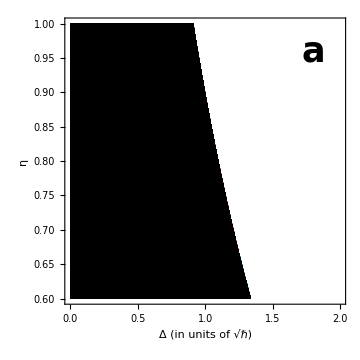

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that dyning is better to simulate certain threshold efficiencies. *)
ClearAll[Δx, α,r,t,θ,η,x1,p1,x2,p2,s, plotpoints];
t=√0.8;
r=√(1-t^2);
θ=0;
α=2;
s=1;
ℱmin=0.6;
"Dyne efficiency chosen:"
ηH =.85
plotpoints=90;
Δlimit =2;
ηlimit = ℱmin;
cols=Reverse[RGBColor/@{(*"#053061","#2166ac",*)"#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d"(*,"#b2182b","#67001f"*)}];
"HOMODYNE:"
text=Text[Style["a",{FontSize->35,FontFamily->"CMU Sans Serif",Black,Bold}],{4.5/5 Δlimit,ηlimit+.9(1-ηlimit)},{0,0}];
txt=Graphics[{text}];
plotROHOM = DensityPlot[UnitStep[Re[fidelityZPSHOM [Δ,δHOM[ηH],r,α,θ,s]]-ℱmin]UnitStep[Re[fidelityZPSTHR[r,α,θ,η,s]]-ℱmin]HeavisideTheta[Re[fidelityZPSHOM [Δ,δHOM[ηH],r,α,θ,s]-fidelityZPSTHR[r,α,θ,η,s]]],{Δ,0,Δlimit},{η,ηlimit,1},PlotPoints->plotpoints,ColorFunction->(Blend[cols,#]&),ColorFunctionScaling->True,PlotRange->All,FrameLabel->{"Δ (in units of √ℏ)","η"},LabelStyle->{FontSize->Large,FontFamily->"CMU Sans Serif",Black},ImageSize->Medium];
plotRIHOM=DensityPlot[HeavisideTheta[Re[PsHOM[Δ,δHOM[ηH],r,α,θ,s]-PsTHR[r,α,η,s]]],{Δ,0,Δlimit},{η,ηlimit,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{"Δ (in units of √ℏ)","η"},LabelStyle->{FontSize->Large,FontFamily->"CMU Sans Serif",Black},ImageSize->Medium];
Show[{plotROHOM,plotRIHOM,txt}]
ClearAll[Δx, α,r,t,θ,η,x1,p1,x2,p2,s, plotpoints];
```

```mathematica
Simplify[Simplify[Total[2π Table[Simplify[V[s,1][[i]]GaussIntR2[v[[i]]unHETwoPrefactor[[j]],x1, p1],{δ>0,s^2==1,t^2==1-r^2,0<r<1}],{i, 1 ,4},{j , 1 ,4}]/.{(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])->(Subscript[f, δ]^Δx)[ⅈ Subscript[α, i]],
(Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))])->(Subscript[f, δ]^Δx)[Subscript[α, r]],
(Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))])->(Subscript[f, δ]^Δp)[ⅈ Subscript[α, r]],
(Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))])->(Subscript[f, δ]^Δp)[Subscript[α, i]]
}
,2]]
/.t^2->1-r^2]
```

(ⅇ^(-2 r^2 α^2) (1+ⅇ^(4 (-1+r^2) α^2)+2 ⅇ^(2 (-1+r^2) α^2) s) (ⅇ^(2 r^2 α^2) f_δ^Δp[ⅈ α_r] f_δ^Δx[ⅈ α_i]+f_δ^Δp[α_i] f_δ^Δx[α_r]))/(4+4 ⅇ^(2 (-1+r^2) α^2) s)

```mathematica
fidelityZPSHET [Δx_,Δp_,δ_,r_,α_,θ_,s_]:=(1+ⅇ^(4 (-1+r^2) α^2)+s 2 ⅇ^(2 (-1+r^2) α^2))/(PsHET[Δx,Δp, δ,r,α,θ,s]8 (1+s ⅇ^(-2 α^2))(1+s ⅇ^(2 (-1+r^2) α^2) ))( (Erf[(Δp-2 √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 √2 r α Cos[θ])/(2 √(1+2 δ))])(Erf[(Δx-2 √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 √2 r α Sin[θ])/(2 √(1+2 δ))])+ⅇ^(-2 r^2 α^2)(Erf[(Δp-2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]+Erf[(Δp+2 ⅈ √2 r α Sin[θ])/(2 √(1+2 δ))]) (Erf[(Δx-2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]+Erf[(Δx+2 ⅈ √2 r α Cos[θ])/(2 √(1+2 δ))]));
```

```mathematica
fidelityZPSHET[2,2,δHOM[0.85],√0.25,2,0,1]
fidelityZPSTHR[√0.25,2,0,0.3,1]
```

0.918688+0. ⅈ

0.624462

```mathematica
PsHET[2,2,δHOM[0.85],√0.25,2,0,1]
PsTHR[√0.25,2,0.3,1]
```

0.23768+0. ⅈ

0.741022

```mathematica
fidelityZPSTHR[√0.25,2,0,0.3,1]
```

0.624462

Dyne efficiency chosen:

0.85

HETERODYNE:

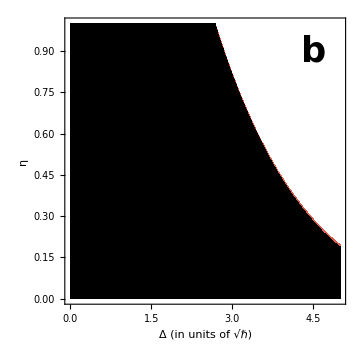

```mathematica
(* Plotting overlap and prob. improvement plots on top of each other. Intersecting lines mean that dyning is better to simulate certain threshold efficiencies. *)
ClearAll[Δx, α,r,t,θ,η,x1,p1,x2,p2,s, plotpoints];
t=√0.75;
r=√(1-t^2);
θ=0;
α=2;
s=1;
"Dyne efficiency chosen:"
ηH =0.85
plotpoints=60;
cols=Reverse[RGBColor/@{(*"#053061","#2166ac",*)"#4393c3","#92c5de","#d1e5f0","#f7f7f7","#fddbc7","#f4a582","#d6604d"(*,"#b2182b","#67001f"*)}];
"HETERODYNE:"
text=Text[Style["b",{FontSize->35,FontFamily->"Arial",Black,Bold}],{4.5,.9},{0,0}];
txt=Graphics[{text}];
plotROHET= DensityPlot[HeavisideTheta[Re[fidelityZPSHET[Δ,Δ,δHET[ηH],r,α,θ,s]-fidelityZPSTHR[r,α,θ,η,s]]],{Δ,0,5},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[cols,#]&),ColorFunctionScaling->True,PlotRange->All,FrameLabel->{"Δ (in units of √ℏ)","η"},LabelStyle->{FontSize->Large,FontFamily->"CMU Sans Serif",Black},ImageSize->Medium];
plotRIHET=DensityPlot[HeavisideTheta[Re[PsHET[Δ,Δ, δHET[ηH],r,α,θ,s]-PsTHR[r,α,η,s]]],{Δ,0,5},{η,0,1},PlotPoints->plotpoints,ColorFunction->(Blend[{RGBColor[0,0,0,0.3],RGBColor[1,1,1,0]},#]&),ColorFunctionScaling->False,PlotRange->All,FrameLabel->{"Δ (in units of √ℏ)","η"},LabelStyle->{FontSize->Large,FontFamily->"CMU Sans Serif",Black},ImageSize->Medium];
Show[{plotROHET,plotRIHET,txt}]
ClearAll[Δx, α,r,t,θ,η,x1,p1,x2,p2,s, plotpoints];
```